## 1d optimal control (Example 7.1 & Problem 7.3)

```mathematica
Clear["Global`*"];
SetOptions[ListPlot,Joined->True,InterpolationOrder->0,PlotRange -> All];
SetOptions[Plot,PlotRange -> All];
```

Example 7.1 calculations

```mathematica
x=ⅇ^(-(a+Kp)t); u = -Kp x; V=1/2(x^2+R u^2);
J=Integrate[V,{t,0,∞}, Assumptions->Re[a+Kp]>0]
```

(1+Kp^2 R)/(4 (a+Kp))

```mathematica
dJ=D[J,Kp] // Simplify
```

(-1+2 a Kp R+Kp^2 R)/(4 (a+Kp)^2)

```mathematica
Kp1=Solve[dJ==0,Kp]
```

{{Kp→(-a R-√(R+a^2 R^2))/R},{Kp→(-a R+√(R+a^2 R^2))/R}}

```mathematica
Kpsol=Kp1[[2]]   (* select the positive root for Kp *);
dJ2=D[J,{Kp,2}] // Simplify    (* general expression for 2nd derivative *)
```

(1+a^2 R)/(2 (a+Kp)^3)

```mathematica
dJ2a=dJ2 /. Kpsol // Simplify   (* substitute the positive root *)
```

R^2/(2 √(R (1+a^2 R)))

The second derivative is positive, implying a minimum.
Verify by plotting the solution (for some particular values of a and R).

```mathematica
{Kpsol /.a->1/.R->1    (* value of kp where minimum is found *),
J/.Kpsol/.a->1/.R->1  // Simplify   (* value of J at Kp that minimizes it *)}
```

{{Kp→-1+√2},-1/2+1/(√2)}

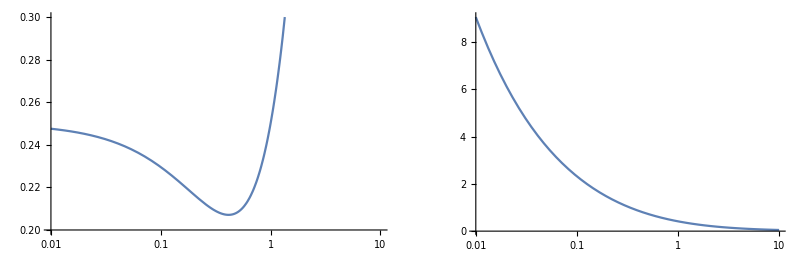

```mathematica
py1=LogLinearPlot[J/.a->1/.R->1,{Kp,0.01,10},PlotRange->{{0.01,10},{0.2,0.3}}];py2=LogLinearPlot[Kp /.Kpsol/.a->1,{R,0.01,10},PlotRange->All];
GraphicsRow[{py1,py2}]
```

Problem 7.3 calculations

```mathematica
a=1;
xx1 =DSolveValue[{xx'[t]+a xx[t]+1==0,xx[0]==x0},xx[t],t]
```

-ⅇ^-t (-1+ⅇ^t-x0)

```mathematica
Solve[{xx1==1/(√2-1)},t] // Simplify
```

{{t→ConditionalExpression[2 ⅈ π C[1]+Log[-1/2 (-2+√2) (1+x0)], C[1]∈ℤ]}}

```mathematica
λ1=DSolveValue[{λ'[t]+a λ[t]+xx1==0,λ[t1]==0},λ[t],t] // Simplify
```

ⅇ^-t (ⅇ^t-ⅇ^t1-(t-t1) (1+x0))

```mathematica
μ=1-λ1
```

1-ⅇ^-t (ⅇ^t-ⅇ^t1-(t-t1) (1+x0))

```mathematica
Solve[μ==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(-2 ⅇ^t1+2 t1+2 t1 x0)/(2 (1+x0))}}

Euler - Lagrange; add final condition that x(τ)=1

```mathematica
j[xτ_,τ_]:=Module[{eq,init,x,λ,t,xs,λs},
eq={
x'[t]==- x[t]-λ[t], 
λ'[t]==  λ[t]-x[t]
};
init={x[0]==0,x[τ]==xτ};
{xs,λs}=DSolveValue[{eq,init},{x,λ},t]//FullSimplify]
```

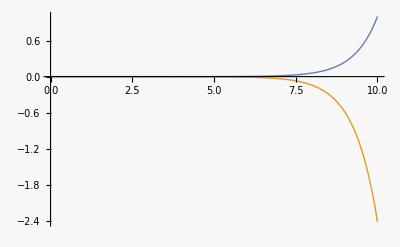

```mathematica
{xs,λs}=j[1,10];
Plot[{xs[t],λs[t]},{t,0,10}]
```

```mathematica
{x1,λ1}=j[xτ,τ]//FullSimplify
```

{Function[{t$1209809},(ⅇ^(-√2 t$1209809+√2 τ) (-1+ⅇ^(2 √2 t$1209809)) xτ)/(-1+ⅇ^(2 √2 τ))],Function[{t$1209809},-(ⅇ^(-√2 t$1209809+√2 τ) (2-√2+2 ⅇ^(2 √2 t$1209809)+√2 ⅇ^(2 √2 t$1209809)) xτ)/(√2 (-1+ⅇ^(2 √2 τ)))]}

```mathematica
a=({{-1, -1}, {-1, 1}});Eigensystem[a]  (* for analytic work *)
```

{{-√2,√2},{{1+√2,1},{1-√2,1}}}

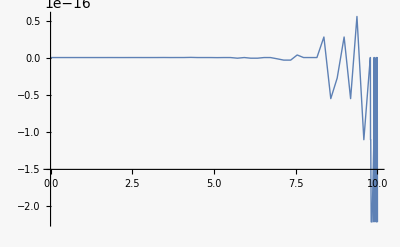

```mathematica
x2[t_,τ_,xτ_]:=xτ Sinh[√2 t]/Sinh[√2 τ]   (* nicer version of solution! *)
Plot[{x2[t,10,1]-x1[t]/.{τ->10,xτ->1}},{t,0,10}]
```

```mathematica
DSolveValue[{λ'[t]==λ[t]+xτ Sinh[√2 t]/Sinh[√2 τ]},λ[t],t]
```

ⅇ^t C[1]+xτ Csch[√2 τ] (√2 Cosh[√2 t]+Sinh[√2 t])